```mathematica
pt[n_,s_]:=((1-s)n^s HarmonicNumber[n,s]-s n^(1-s) HarmonicNumber[n,1-s])/((1-s)n^s - s n^(1-s))
pt2[n_,s_]:=((1-s)n^s (Zeta[s]-Zeta[s,n+1])-s n^(1-s)( Zeta[1-s]-Zeta[1-s,n+1]))/((1-s)n^s - s n^(1-s))
pt2a[n_,s_]:=((1-s)n^s (Zeta[s])-s n^(1-s)( Zeta[1-s]))/((1-s)n^s - s n^(1-s))
pt2a1[n_,s_]:=((1-s)n^s (Zeta[s]))/((1-s)n^s - s n^(1-s))
pt2a2[n_,s_]:=(-s n^(1-s)( Zeta[1-s]))/((1-s)n^s - s n^(1-s))
pt2a2b[n_,s_]:=(-Zeta[1-s])/((1-s)/s n^(2 s-1) - 1)
pt2a2c[n_,s_]:=Zeta[1-s]/(1-(1-s)/s n^(2 s-1))
pt2a2d[n_,s_]:=1/(1-(1-s)/s n^(2 s-1))
pt2b[n_,s_]:=((1-s)n^s (-Zeta[s,n+1])-s n^(1-s)( -Zeta[1-s,n+1]))/((1-s)n^s - s n^(1-s))
pt2bx[n_,s_]:=((1-s)n^s (-Zeta[s,n+1])-s n^(1-s)( -Zeta[1-s,n+1]))
pt2b1[n_,s_]:=((1-s)n^s (-Zeta[s,n+1]))/((1-s)n^s - s n^(1-s))
pt2b2[n_,s_]:=(-s n^(1-s)( -Zeta[1-s,n+1]))/((1-s)n^s - s n^(1-s))
pt2b1a[n_,s_]:=((1-s)n^s (-Zeta[s,n+1]))
pt2b2a[n_,s_]:=(-s n^(1-s)( -Zeta[1-s,n+1]))
pt2b2as[n_,s_,t_]:=pt2b1a[n,s]-pt2b1a[n,t]
pt2b2at[n_,s_,t_]:=pt2b1a[n,s]+pt2b2a[n,t]
pt2b2ax[n_,s_,t_]:=((1-s)n^s (-Zeta[s,n+1]))-((1-t)n^t (-Zeta[t,n+1]))
pt2bz[n_,s_]:=((1-s)n^s (-Zeta[s,n+1])-s n^(1-s)( -Zeta[1-s,n+1]))
pt2by[n_,s_]:=((1-s)n^s (-Zeta[s,n+1])-s n^(1-s)( -Zeta[1-s,n+1]))
pt2ay[n_,s_]:=n^(-.5)((1-s)n^s (Zeta[s])-s n^(1-s)( Zeta[1-s]))
ff[n_,s_]:=(1-s)n^s
pto[n_,s_]:=(ff[n,s] HarmonicNumber[n,s]-ff[n,1-s] HarmonicNumber[n,1-s])/(ff[n,s] - ff[n,1-s])
pto2[n_,s_,t_]:=(ff[n,s] HarmonicNumber[n,s]-ff[n,t] HarmonicNumber[n,t])/(ff[n,s] - ff[n,t])
```

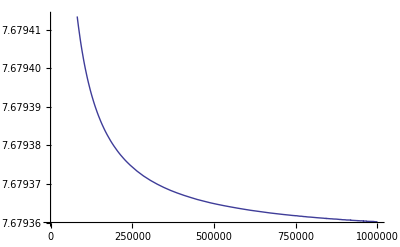

```mathematica
Plot[Abs@pt2b2as[n,-3+15I,.3],{n,1,1000000}]
```

```mathematica
pt2a1[1000000000000,.9]
```

-9.43011

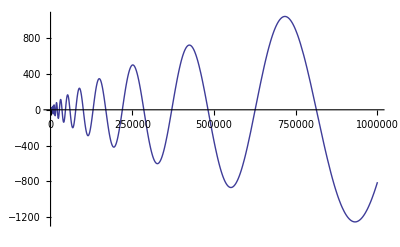

```mathematica
Plot[{Re@Zeta[.3+12I,n+1]},{n,1,1000000}]
```

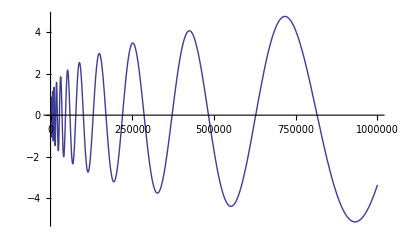

```mathematica
Plot[{Re@Zeta[.7-12I,n+1]},{n,1,1000000}]
```

```mathematica
pto2[10000000000,-.4,-1]
```

-2143.1

```mathematica
Zeta[-.4]
```

-0.247165

```mathematica
HarmonicNumber[n,0]
```

n

```mathematica
FullSimplify[pto2[n,s,-1]]
```

(n (1+n+n^s (-1+s) HarmonicNumber[n,s]))/(2+n^(1+s) (-1+s))

```mathematica
FullSimplify[(n+n^s (-1+s))/(1+n^s (-1+s))]
```

1+(-1+n)/(1+n^s (-1+s))

```mathematica
Zeta[.3]
```

-0.904559

```mathematica
pr[n_,s_]:=(n+n^s (-1+s) HarmonicNumber[n,s])/(1+n^s (-1+s))
pra[n_,s_]:={(n^s (-1+s) HarmonicNumber[n,s])/(1+n^s (-1+s)),n/(1+n^s (-1+s))}
prb[n_,s_]:=n/(1+n^s (-1+s))+Sum[(n^s (-1+s) j^-s)/(1+n^s (-1+s)),{j,1,n}]
prc[n_,s_]:=n/(1+n^s (-1+s))+Sum[1/(j^s+(j^s n^-s)/(-1+s)),{j,1,n}]
prk[n_,s_]:=(n (1+n+n^s (-1+s) HarmonicNumber[n,s]))/(2+n^(1+s) (-1+s))
```

```mathematica
FullSimplify[prc[n,s]]
```

n/(1+n^s (-1+s))+∑_(j=1)^n 1/(j^s+(j^s n^-s)/(-1+s))

```mathematica
Zeta[.7+1000I]
```

0.784054+0.374829 ⅈ

```mathematica
FullSimplify[(n+n^s (-1+s) HarmonicNumber[n,s])/(1+n^s (-1+s))]
```

(n+n^s (-1+s) HarmonicNumber[n,s])/(1+n^s (-1+s))

```mathematica
FullSimplify[n/(1+n^s (-1+s))]
```

n/(1+n^s (-1+s))

```mathematica
FullSimplify[(n^s (-1+s) j^-s)/(1+n^s (-1+s))]
```

1/(j^s+(j^s n^-s)/(-1+s))

```mathematica
N@prk[10000000000,1/2]
```

-1.46037

```mathematica
Zeta[.5]
```

-1.46035

```mathematica
FullSimplify[HarmonicNumber[n,-1]]
```

1/2 n (1+n)

```mathematica
pr[n,s]
```

(n+n^s (-1+s) HarmonicNumber[n,s])/(1+n^s (-1+s))

```mathematica
prx[n_,s_,a_]:=(n^a+n^s (-1+s) HarmonicNumber[n,s]^a)/(1+n^s (-1+s))
```

```mathematica
prk[10000000,-.5]
```

-527.477

```mathematica
pto3[n_,s_,t_]:=(ff[n,s] HarmonicNumber[n,s]-ff[n,t] HarmonicNumber[n,t])/ff[n,s]
```

```mathematica
FullSimplify[pto3[n,s,-1]]
```

(n^-s (1+n))/(-1+s)+HarmonicNumber[n,s]

```mathematica
Zeta[.7]
```

-2.77839

```mathematica
pto3[1000000,.7,-4]
```

-2.77888

```mathematica
pt[n_,s_]:=((1-s)n^s HarmonicNumber[n,s]-s n^(1-s) HarmonicNumber[n,1-s])/((1-s)n^s - s n^(1-s))
et[n_,s_]:=((1-s)n^s HarmonicNumber[n,s]-(1-s)n^s HarmonicNumber[n,1-s])/((1-s)n^s - s n^(1-s))
pt2b2ax[n_,s_,t_]:=((1-s)n^s (-Zeta[s,n+1]))-((1-t)n^t (-Zeta[t,n+1]))
```

```mathematica
et[100000,.9]
```

-35145.4

```mathematica
Zeta[.9]
```

-9.43011

```mathematica
pt2b2ax[100000,.9,.8]
```

-0.0499999

```mathematica
fa[n_,s_]:=(1-s)n^s
prt[n_,s_,t_]:=(ff[n,s] HarmonicNumber[n,s]-ff[n,t] HarmonicNumber[n,t])/(ff[n,s])
prt2[n_,s_,t_]:=HarmonicNumber[n,s]-ff[n,t]/(ff[n,s]) HarmonicNumber[n,t]
```

```mathematica
prt2[1000000000,.6,.3]
```

-1.9495

```mathematica
Zeta[.6]
```

-1.95266

```mathematica
FullSimplify[fa[n,1-s]/fa[n,s]]
```

(n^(1-2 s) s)/(1-s)

```mathematica
pb[n_,s_]:= n^-s/(s-1/2) Sum[ j^(-1/2)(2 s Cosh[s Log[n/j]] - Sinh[s Log[n/j]]),{j,1,n}]
```

```mathematica
pb[1000000,.3+7I]
```

1.02523+0.338313 ⅈ

```mathematica
Zeta[.8+7I]
```

1.02505+0.338122 ⅈ

```mathematica
prt[1000000000,.8+7I,1-(.8+7I)]
```

1.02505+0.338117 ⅈ

```mathematica
FullSimplify[Cos[ t Log[j]]+((t Sin[t Log[n]]+(1/2)Cos[t Log[n]])/(t Cos[t Log[n]]-(1/2)Sin[t Log[n]]))Sin[t Log[j]]]
```

(2 t Cos[t (Log[j]-Log[n])]+Sin[t (Log[j]-Log[n])])/(2 t Cos[t Log[n]]-Sin[t Log[n]])

```mathematica
pr[n_,t_]:=((t Sin[t Log[n]]+(1/2)Cos[t Log[n]])/(t Cos[t Log[n]]-(1/2)Sin[t Log[n]]))
```

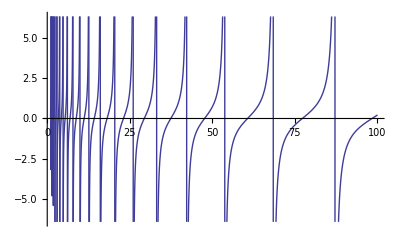

```mathematica
Plot[ pr[n,13],{n,1,100}]
```

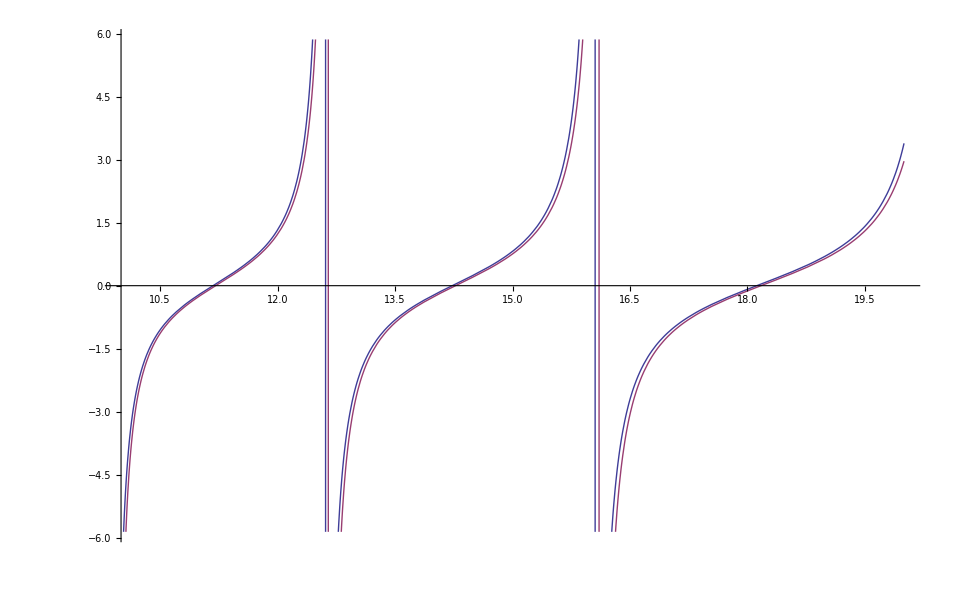

```mathematica
Plot[{pr[n,13], Tan[13 Log[n]]},{n,10,20}]
```

```mathematica
pr[n_,t_]:=((t Sin[t Log[n]]+(1/2)Cos[t Log[n]])/(t Cos[t Log[n]]-(1/2)Sin[t Log[n]]))
prs[n_,t_]:=((t/(2I) (n^(I t )-n^(-I t ))+(1/2)Cos[t Log[n]])/(t Cos[t Log[n]]-(1/2)Sin[t Log[n]]))
prst[n_,t_]:=((2t/(I) (n^(I t )-n^(-I t ))+(n^(I t)+n^(-I t)))/(2t (n^(I t)+n^(-I t))-(1/ I)(n^(I t)-n^(-I t))))
prst1[n_,t_]:=((-2t I (n^(I t )-n^(-I t ))+(n^(I t)+n^(-I t)))/(2t (n^(I t)+n^(-I t))+I(n^(I t)-n^(-I t))))
```

```mathematica
prst1[100,.3]
```

-0.894314+0. ⅈ

```mathematica
((-2t I (n^(I t )-n^(-I t ))+(n^(I t)+n^(-I t)))/(2t (n^(I t)+n^(-I t))+I(n^(I t)-n^(-I t))))
```

(n^(-ⅈ t)+n^(ⅈ t)-2 ⅈ (-n^(-ⅈ t)+n^(ⅈ t)) t)/(ⅈ (-n^(-ⅈ t)+n^(ⅈ t))+2 (n^(-ⅈ t)+n^(ⅈ t)) t)

```mathematica
1/I
```

-ⅈ

```mathematica
ba[n_,s_]:= Sum[ (1-s)(n/j)^s-s (j/n)^(s-1),{j,1,n}]
ba2[n_,s_]:= (1-s)n^s HarmonicNumber[ n,s]-s n^(1-s) HarmonicNumber[ n,1-s]
ba3[n_,s_]:= -n^(1/2-s) (1/2+s) HarmonicNumber[n,1/2-s]+n^(1/2+s) (1/2-s) HarmonicNumber[n,1/2+s]
ba4[n_,s_]:=Sum[ (n/j)^(1/2+s) (1/2-s)-(j/n)^(-1/2+s) (1/2+s),{j,1,n}]
ba5[n_,s_]:=-I(n^(1/2-ⅈ s) (1/2+ⅈ s) HarmonicNumber[n,1/2-ⅈ s]-n^(1/2+ⅈ s) (1/2-ⅈ s) HarmonicNumber[n,1/2+ⅈ s])
ba5a[n_,s_]:=-I(n^(1/2-ⅈ s) (1/2+ⅈ s) HarmonicNumber[n,1/2-ⅈ s])
ba5b[n_,s_]:=-I(n^(1/2+ⅈ s) (1/2-ⅈ s) HarmonicNumber[n,1/2+ⅈ s])
ba5ax[n_,s_]:=-I(n^(1/2-ⅈ s) (1/2+ⅈ s) HarmonicNumber[n,1/2-ⅈ s])/n^(1/2)
ba5bx[n_,s_]:=-I(n^(1/2+ⅈ s) (1/2-ⅈ s) HarmonicNumber[n,1/2+ⅈ s])/n^(1/2)
ba6[n_,s_]:=-I Sum[ (j/n)^(-1/2+I s) (1/2+I s)-(n/j)^(1/2+I s) (1/2-I s),{j,1,n}]
ba7[n_,s_]:=-I Sum[ (n/j)^(1/2-I s) (1/2+I s)-(n/j)^(1/2+I s) (1/2-I s),{j,1,n}]
ba7a[n_,s_]:=Sum[ (n/j)^(1/2+I s) (1/2 I+s)-(n/j)^(1/2-I s) (1/2 I- s),{j,1,n}]
ba8[n_,s_,a_]:=Sum[ (n/j)^(a+I s) (a I+s)-(n/j)^(a-I s) (a I- s),{j,1,n}]
```

```mathematica
ba7a[100000000,N@Im@ZetaZero@20]
```

77.1448+0. ⅈ

```mathematica
ba2[n,s+1/2]
```

-n^(1/2-s) (1/2+s) HarmonicNumber[n,1/2-s]+n^(1/2+s) (1/2-s) HarmonicNumber[n,1/2+s]

```mathematica
(1-s)(n/j)^s-s (j/n)^(s-1)/.s->s+1/2
```

(n/j)^(1/2+s) (1/2-s)-(j/n)^(-1/2+s) (1/2+s)

```mathematica
ba2[n,-s I+1/2]
```

n^(1/2-ⅈ s) (1/2+ⅈ s) HarmonicNumber[n,1/2-ⅈ s]-n^(1/2+ⅈ s) (1/2-ⅈ s) HarmonicNumber[n,1/2+ⅈ s]

```mathematica
N@Im@ZetaZero@1-1/2I
```

14.1347-0.5 ⅈ

```mathematica
(N@ZetaZero@1-1/2)I
```

-14.1347+0. ⅈ

```mathematica
ba7[n,x]
```

$Aborted

```mathematica
ba8[10000000,N@Im@ZetaZero@1,0]
```

1.40793×10^6+0. ⅈ

```mathematica
N@Im@ZetaZero@120
```

269.97

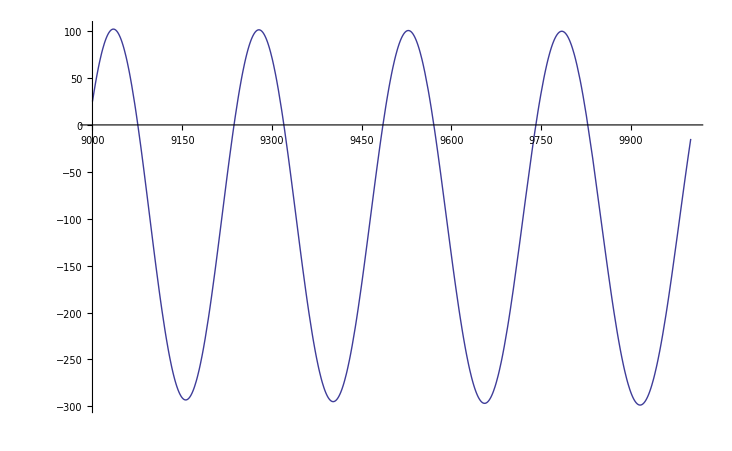

```mathematica
Plot[Im@ba5ax[n,Im@ZetaZero@100+.1I],{n,9000,10000}]
```

```mathematica
D[(n/j)^(1/2+I s) (1/2 I+s)-(n/j)^(1/2-I s) (1/2 I- s),s]
```

(n/j)^(1/2-ⅈ s)+(n/j)^(1/2+ⅈ s)+ⅈ (n/j)^(1/2-ⅈ s) (ⅈ/2-s) Log[n/j]+ⅈ (n/j)^(1/2+ⅈ s) (ⅈ/2+s) Log[n/j]

```mathematica
ba7ax[n_,s_]:=Table[ {(n/j)^(1/2+I s) (1/2 I+s),(n/j)^(1/2-I s) (1/2 I- s)},{j,1,n}]
ba7ay[n_,s_]:=DiscretePlot[{Re[ (n/j)^(1/2+I s) (1/2 I+s)-(n/j)^(1/2-I s) (1/2 I- s)],Im[ (n/j)^(1/2+I s) (1/2 I+s)-(n/j)^(1/2-I s) (1/2 I- s)]},{j,1,n}]
```

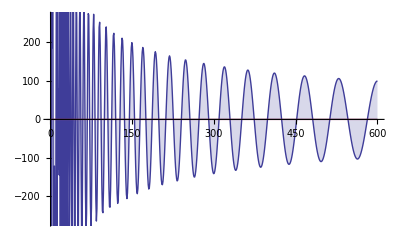

```mathematica
ba7ay[600,N@Im@ZetaZero@10+.1]
```

```mathematica
ba7a[n_,x_]:=Sum[ ((n/j)^((1/2)+I x) (1/2 I+x)-(n/j)^((1/2)-I x) (1/2 I- x)),{j,1,n}]
ba7b[n_,x_]:=Sum[ (n/j)^(1/2)(2 x Cos[ x Log[n/j]]-Sin[x Log[n/j]]),{j,1,n}]
ba7c[n_,x_]:=n^(1/2)((2 x Sin[ x Log[n]]+Cos[x Log[n]])Sum[ (j)^(-1/2)Sin[x Log[j]],{j,1,n}]+(2 x Cos[ x Log[n]]-Sin[x Log[n]])Sum[ (j)^(-1/2)Cos[x Log[j]],{j,1,n}])
ba7d[n_,x_]:=Sum[ j^(-1/2)((n/j)^(+I x) (1/2 I+x)-(n/j)^(-I x) (1/2 I- x)),{j,1,n}]
div[n_,x_]:=(1/2-x I)n^(1/2+x I)-(1/2+x I)n^(1/2-x I)2^(1/2-x I)Pi^(-1/2-x I)Cos[ Pi/4+Pi x I/2]Gamma[1/2+x I]
div2[n_,x_]:=2^(1/2+ⅈ x) n^(1/2+ⅈ x) π^(-1/2+ⅈ x) (1/2 I+x) Cos[1/2 π (1/2-ⅈ x)] Gamma[1/2-ⅈ x]-n^(1/2-ⅈ x) (1/2 I-x)
```

```mathematica
ba7a[1000000000000,N@Im@ZetaZero@1]
```

0.896724+0. ⅈ

```mathematica
ba7b[10000,.3-.1I]
```

40.4575+167.902 ⅈ

```mathematica
ba7c[10000,.3-.1I]
```

40.4575+167.902 ⅈ

```mathematica
1-(1/2+x I)
```

1/2-ⅈ x

```mathematica
ba7a[1000000000000,.3I+10]/div2[1000000000000,.3I+10]
```

1.44628+0.113501 ⅈ

```mathematica
Zeta[.8+10I]
```

1.44628-0.113501 ⅈ

```mathematica
pa11[n_,s_]:= (n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s])(2 n^(1-s) s(2 π)^-s Cos[(π s)/2] Gamma[s]-n^s  (1-s))^-1
pa11a[n_,s_]:= (n^s (1-s) HarmonicNumber[n,s]-n^(1-s) s HarmonicNumber[n,1-s])/(n^s  (1-s)-2 n^(1-s) s(2 π)^-s Cos[(π s)/2] Gamma[s])
pa11b[n_,x_]:= (n^(1/2-ⅈ x) (1/2+ⅈ x) HarmonicNumber[n,1/2-ⅈ x]-n^(1/2+ⅈ x) (1/2-ⅈ x) HarmonicNumber[n,1/2+ⅈ x])/(n^(1/2-ⅈ x) (1/2+ⅈ x)-2^(1/2+ⅈ x) n^(1/2+ⅈ x) π^(-1/2+ⅈ x) (1/2-ⅈ x) Cos[1/2 π (1/2-ⅈ x)] Gamma[1/2-ⅈ x])
pa11c[n_,x_]:= (n^(1/2+ⅈ x) (1/2-ⅈ x) HarmonicNumber[n,1/2+ⅈ x]-n^(1/2-ⅈ x) (1/2+ⅈ x) HarmonicNumber[n,1/2-ⅈ x])/(n^(1/2-ⅈ x) (1/2-ⅈ x)-2^(1/2+ⅈ x) n^(1/2+ⅈ x) π^(-1/2+ⅈ x) (1/2+ⅈ x) Cos[1/2 π (1/2-ⅈ x)] Gamma[1/2-ⅈ x])
pa11d[n_,x_]:= (n^(1/2-ⅈ x) (1/2 I- x) HarmonicNumber[n,1/2-ⅈ x]-n^(1/2+ⅈ x) (1/2 I+ x) HarmonicNumber[n,1/2+ⅈ x])/(n^(1/2-ⅈ x) (1/2 I-x)-2^(1/2+ⅈ x) n^(1/2+ⅈ x) π^(-1/2+ⅈ x) (1/2 I+x) Cos[1/2 π (1/2-ⅈ x)] Gamma[1/2-ⅈ x])
zeta[n_,s_]:=pa11d[n,(s I-.5I)]
pa11da[n_,x_]:= n^(1/2-ⅈ x) (1/2 I- x) HarmonicNumber[n,1/2-ⅈ x]-n^(1/2+ⅈ x) (1/2 I+ x) HarmonicNumber[n,1/2+ⅈ x]
pa11e[n_,x_]:= (n^(1/2+ⅈ x) (1/2 I+ x) HarmonicNumber[n,1/2+ⅈ x]-n^(1/2-ⅈ x) (1/2 I- x) HarmonicNumber[n,1/2-ⅈ x])/(2^(1/2+ⅈ x) n^(1/2+ⅈ x) π^(-1/2+ⅈ x) (1/2 I+x) Cos[1/2 π (1/2-ⅈ x)] Gamma[1/2-ⅈ x]-n^(1/2-ⅈ x) (1/2 I-x))
zetae[n_,s_]:=pa11e[n,(s -.5)I]
pa11ea[n_,x_]:= n^(1/2+ⅈ x) (1/2 I+ x) HarmonicNumber[n,1/2+ⅈ x]-n^(1/2-ⅈ x) (1/2 I- x) HarmonicNumber[n,1/2-ⅈ x]
```

```mathematica
pa11a[n,1/2-x I]
```

(n^(1/2-ⅈ x) (1/2+ⅈ x) HarmonicNumber[n,1/2-ⅈ x]-n^(1/2+ⅈ x) (1/2-ⅈ x) HarmonicNumber[n,1/2+ⅈ x])/(n^(1/2-ⅈ x) (1/2+ⅈ x)-2^(1/2+ⅈ x) n^(1/2+ⅈ x) π^(-1/2+ⅈ x) (1/2-ⅈ x) Cos[1/2 π (1/2-ⅈ x)] Gamma[1/2-ⅈ x])

```mathematica
Zeta[.8+3I]
```

0.590541-0.0980708 ⅈ

```mathematica
pa11d[1000000000,.9I-.5I-3]
```

0.609764-0.103129 ⅈ

```mathematica
Zeta[.55+113I]
```

1.4668+0.67276 ⅈ

```mathematica
pa11a[n,s]
```

(-n^(1-s) s HarmonicNumber[n,1-s]+n^s (1-s) HarmonicNumber[n,s])/(n^s (1-s)-2^(1-s) n^(1-s) π^-s s Cos[(π s)/2] Gamma[s])

```mathematica
zetae[1000000000,.55+113I]
```

1.4668+0.672773 ⅈ

```mathematica
pa11ea[100000,N@Im@ZetaZero@11]
```

52.9703+0. ⅈ

```mathematica
N@Im@ZetaZero@11
```

52.9703

```mathematica
FullSimplify[2^(1/2+ⅈ x) n^(1/2+ⅈ x) π^(-1/2+ⅈ x) ]
```

2^(1/2+ⅈ x) n^(1/2+ⅈ x) π^(-1/2+ⅈ x)

```mathematica
pa11f[n_,x_]:= (n^(ⅈ x) (1/2 I+ x) HarmonicNumber[n,1/2+ⅈ x]-n^(-ⅈ x) (1/2 I- x) HarmonicNumber[n,1/2-ⅈ x])/(2^(1/2+ⅈ x) n^(ⅈ x) π^(-1/2+ⅈ x) (1/2 I+x) Sin[Pi/4 + 2 Pi I x/4] Gamma[1/2-ⅈ x]-n^(-ⅈ x) (1/2 I-x))
pa11f2[n_,x_]:= n^(ⅈ x) (1/2 I+ x) HarmonicNumber[n,1/2+ⅈ x]-n^(-ⅈ x) (1/2 I- x) HarmonicNumber[n,1/2-ⅈ x]
zetaf[n_,s_]:=pa11f[n,(s -1/2)I]
```

```mathematica
zetaf[1000000,.77+44I]
```

0.466395+1.07449 ⅈ

```mathematica
Zeta[.77+44I]
```

0.466395+1.07447 ⅈ

```mathematica
FullSimplify@Cos[1/2 π (1/2-ⅈ x)]
```

Sin[1/4 (π+2 ⅈ π x)]

```mathematica
FullSimplify[(2^(1/2+ⅈ x) n^(ⅈ x) π^(-1/2+ⅈ x) )^(-I x)]
```

(2^(1/2+ⅈ x) n^(ⅈ x) π^(-1/2+ⅈ x))^(-ⅈ x)

```mathematica
2^(1/2+I x)/2^(I x)
```

√2

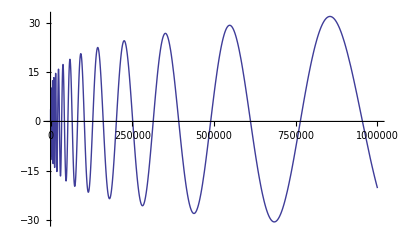

```mathematica
Plot[Im@pa11f2[n,N@Im@ZetaZero@1+.2I],{n,1,1000000}]
```